```mathematica
(1/(80*365))/((1/(80*365))+1/365)
```

1/81

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

(1/81 (-1+R)+1/81 √((-1+R)^2+4 p R))/(2 R)

```mathematica
ϵ=1/81
```

1/81

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→(-1036800 R+1200562 R^2-136161 R^3-72 √10 √(-92294440 R^2+293894601 R^3-311859120 R^4+110273600 R^5))/(11303044 R^2)},{p→(-1036800 R+1200562 R^2-136161 R^3+72 √10 √(-92294440 R^2+293894601 R^3-311859120 R^4+110273600 R^5))/(11303044 R^2)}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=(-1036800 R+1200562 R^2-136161 R^3+72 √10 √(-92294440 R^2+293894601 R^3-311859120 R^4+110273600 R^5))/(11303044 R^2)
```

```mathematica
h[R_]:=g[R-1]
```

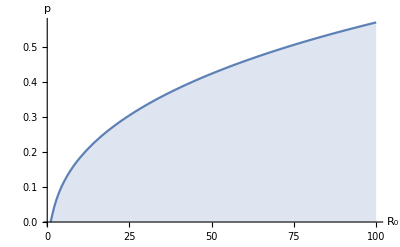

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

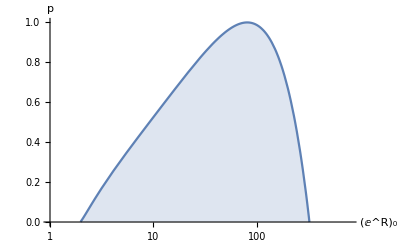

```mathematica
LogLinearPlot[h[R],{R,0.001,800},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->{{0,800},{0,1}}]
```

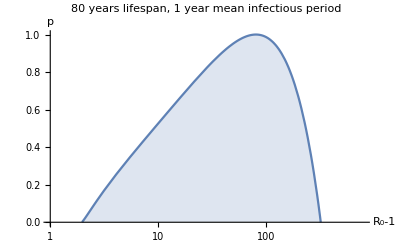

```mathematica
Show[%86,AxesLabel->{HoldForm[Subscript[R, 0]-1],p},PlotLabel->RawBoxes[RowBox[{RowBox[{"80"," ","years"," ","lifespan"}],","," ",RowBox[{"1"," ","year"," ","mean"," ","infectious"," ","period"}]}]],LabelStyle->{GrayLevel[0]}]
```